# Poincaré sphere and polarization ellipse visuals

P. Huft

## functions - run first

```mathematica
PoincareSphereVectorFromStokesParameters[s1_,s2_,s3_,labelSize_:20]:=Graphics3D[{{Specularity[Pink,5],Opacity[0.1],Sphere[]},{Red,Thick,Arrow[{{0,0,0},{s1,s2,s3}}]},{Blue,Thick,Dashed,Line[{{0,0,0},{s1,s2,0}}]},
{Blue,Thick,Dashed,Line[{{s1,s2,0},{s1,s2,s3}}]},{Green,Thick,Dashed,Line[{{0,0,0},{0,0,s3}}]},
{Green,Thick,Dashed,Line[{{0,0,s3},{s1,s2,s3}}]},Text[Style["R",labelSize],{0,0,1.3}],Text[Style["L",labelSize],{0,0,-1.3}],Text[Style["H",labelSize],{1.3,0,0}],Text[Style["V",labelSize],{-1.3,0,0}],Text[Style["D",labelSize],{0,1.3,0}],Text[Style["A",labelSize],{0,-1.3,0}]},Boxed->False,Axes->True,AxesOrigin->{0,0,0},ImageSize->Large];
```

I was trying to add a circle to the sphere so it’s easier to see what height the vector is when it happens to be eclipsed by the z (s3) axis, but it turns out to be tricky. PoincareSphereLongitude below should work if I can get the parameters to evaluate. I was able to get the circle to show up using specific values in the function in place of s1,2,3.

```mathematica
(*this doesn't work https://mathematica.stackexchange.com/questions/79524/how-to-draw-a-circle-in-3d-on-a-sphere*)
(*Circle3D[centre_:{0,0,0},radius_:1,normal_:{0,0,1},angle_:{0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle>=2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]];*)

(*https://resources.wolframcloud.com/FunctionRepository/resources/Circle3D/*)
Clear[Circle3D];
(*Circle3D[]:=Cases[ParametricPlot3D[{0,Sin[t],Cos[t]},{t,-π,π}],_Line,∞];
Circle3D[{a_,b_}]:=Cases[ParametricPlot3D[{0,a Sin[t],b Cos[t]},{t,-π,π}],_Line,∞];*)
Circle3D[c:{_,_,_},{a_,b_},ψ_:0,ζ_:0]:=Cases[ParametricPlot3D[c+{-a Cos[ψ] Sin[t] Sin[ζ]+b Cos[t] Sin[ψ],a Cos[ζ] Sin[t],b Cos[t] Cos[ψ]+a Sin[t] Sin[ζ] Sin[ψ]},{t,-π,π}],_Line,∞];

(*PoincareSphereVectorFromStokesParameters[s1_,s2_,s3_]:=Graphics3D[{{Specularity[Pink,5],Opacity[0.1],Sphere[]},{Red,Thick,Arrow[{{0,0,0},{s1,s2,s3}}]},{Blue,Thick,Dashed,Line[{{0,0,0},{s1,s2,0}}]},
{Blue,Thick,Dashed,Line[{{s1,s2,0},{s1,s2,s3}}]},{Green,Thick,Dashed,Line[{{0,0,0},{0,0,s3}}]},
{Green,Thick,Dashed,Line[{{0,0,s3},{s1,s2,s3}}]},Text[Style["R",20],{0,0,1.3}],Text[Style["L",20],{0,0,-1.3}],Text[Style["H",20],{1.3,0,0}],Text[Style["V",20],{-1.3,0,0}],Text[Style["D",20],{0,1.3,0}],Text[Style["A",20],{0,-1.3,0}]},Boxed->False,Axes->True,AxesOrigin->{0,0,0},ImageSize->Large];
*)
PoincareSphereLongitude[s1_,s2_,s3_]:=ParametricPlot3D[Evaluate[{√(s1^2+s2^2)Sin[u],√(s1^2+s2^2)Cos[u],s3}],{u,0,2π},PlotStyle->Directive[Thick,Dashed,Orange],PlotRange->All,Boxed->False];
```

```mathematica
Table
```

Table

## visualizing polarization on the Poincaré sphere and the polarization ellipse

Consider an input state which is rotated first by a quarter waveplate and subsequently a half waveplate.

```mathematica
R[θ_]:=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}});(*kindergarten-level rotation matrix*)
qwp=({{1, 0}, {0, ⅈ}});(*quarter waveplate with vertical fast axis. from Fowles*)
hwp=({{1, 0}, {0, -1}});(*half waveplate with either horizontal or vertical fast axis. from Fowles*)
QWP[θ_]:=R[θ].qwp.Inverse[R[θ]];(*waveplate with fast axis angle θ from vertical*)
HWP[θ_]:=R[θ].hwp.Inverse[R[θ]];(*waveplate with fast axis angle θ from vertical*)

(*some polarization states*)
Ex={1,0};
Ey={0,1};
Eplus=1/(√2){1,ⅈ};
Eminus=1/(√2){1,-ⅈ};
```

```mathematica
R[θ].qwp.Inverse[R[θ]]//FullSimplify
```

{{(1/2-ⅈ/2) (ⅈ+Cos[2 θ]),(-1+ⅈ) Cos[θ] Sin[θ]},{(-1+ⅈ) Cos[θ] Sin[θ],ⅈ Cos[θ]^2+Sin[θ]^2}}

```mathematica
R[θ].hwp.Inverse[R[θ]]//FullSimplify
```

{{Cos[2 θ],-2 Cos[θ] Sin[θ]},{-2 Cos[θ] Sin[θ],-Cos[2 θ]}}

```mathematica
Ein=Ex;(*the starting state*)
Eout=HWP[hwpAngleDegrees π/180].QWP[qwpAngleDegrees π/180].Ein;(*the output state after applying rotations*)
ExOut=Eout.Ex;
EyOut=Eout.Ey;
δ=Arg[EyOut]-Arg[ExOut];
s1 =Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
x[t_]=Abs[ExOut]Cos[t];
y[t_]=Abs[EyOut]Cos[t-δ];
polarizationLabelSize=10;
Manipulate[GraphicsGrid[{{Evaluate[PoincareSphereVectorFromStokesParameters[s1,s2,s3,polarizationLabelSize]/.{qwpAngleDegrees->qwpAngle,hwpAngleDegrees->hwpAngle}],Show[ParametricPlot[Evaluate[{x[t],y[t]}/.{qwpAngleDegrees->qwpAngle,hwpAngleDegrees->hwpAngle}],{t,0,2π},PlotRange->{{-1,1},{-1,1}},PlotStyle->Red,AxesLabel->{"Ex","Ey"},LabelStyle->Directive[Black, FontSize->12]],Table[Graphics[{Red,Arrow[{Evaluate[{x[t],y[t]}/.{qwpAngleDegrees->qwpAngle,hwpAngleDegrees->hwpAngle}],Evaluate[{x[t]-Sign[Mod[δ,π]]0.1D[x[τ],τ]/.τ->t,y[t]-Sign[Mod[δ,π]]0.1D[y[τ],τ]/.τ->t}/.{qwpAngleDegrees->qwpAngle,hwpAngleDegrees->hwpAngle}]}]}],{t,0,2π,(2π)/20}]]}},ImageSize->Full],{qwpAngle,0.001,180},{hwpAngle,0.001,180}]
```

## polarization state optimization

```mathematica
R[θ_]:=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}});(*kindergarten-level rotation matrix*)
qwp=({{1, 0}, {0, ⅈ}});(*quarter waveplate with vertical fast axis. from Fowles*)
hwp=({{1, 0}, {0, -1}});(*quarter waveplate with either horizontal or vertical fast axis. from Fowles*)
QWP[θ_]:=R[θ].qwp.Inverse[R[θ]];(*waveplate with fast axis angle θ from vertical*)
HWP[θ_]:=R[θ].hwp.Inverse[R[θ]];(*waveplate with fast axis angle θ from vertical*)

(*some polarization states*)
Ex={1,0};
Ey={0,1};
Eplus=1/(√2){1,ⅈ};
Eminus=1/(√2){1,-ⅈ};
```

```mathematica
Ein=Ex;(*the starting state*)
PolarizationError[linearError_,ellipticalError_]:=HWP[linearError π/180].QWP[ellipticalError π/180];(*some error, e.g. from an optical fiber, on our state*)

(*the output state after applying rotations*)
Manipulate[ContourPlot[Evaluate[Abs[Ex.PolarizationError[linearError,ellipticalError].HWP[hwpAngleDegrees π/180].QWP[qwpAngleDegrees π/180].Ein]],{hwpAngleDegrees,-90,90},{qwpAngleDegrees,-90,90},FrameLabel->{"HWP angle","QWP angle"},Contours->20,PlotLegends->Automatic,PlotLabel->"Ex polarization"],{linearError,0.001,180},{ellipticalError,0.001,180}]
```

## testing

### testing my quarter and half waveplate expressions

These matrices came from wikipedia.

```mathematica
QWP[θ_]:=ⅇ^(-(ⅈ π)/4)({{Cos[θ]^2+ⅈ Sin[θ]^2, (1-ⅈ)Sin[θ]Cos[θ]}, {(1-ⅈ)Sin[θ]Cos[θ], ⅈ Cos[θ]^2+Sin[θ]^2}});
HWP[θ_]:=ⅇ^(-(ⅈ π)/2)({{Cos[θ]^2-Sin[θ]^2, 2Cos[θ] Sin[θ]}, {2Cos[θ]Sin[θ], Sin[θ]^2-Cos[θ]^2}});
```

Work out the results for myself using Fowles:

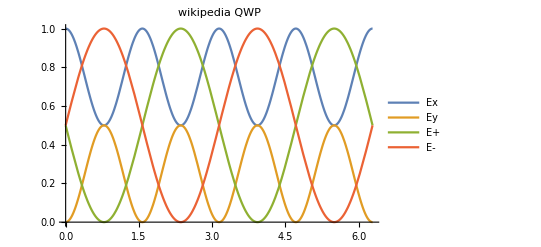

```mathematica
R[θ_]:=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}});
qwp=({{1, 0}, {0, ⅈ}});
hwp=({{1, 0}, {0, -1}});
QWPmine[θ_]:=R[θ].qwp.Inverse[R[θ]];
HWPmine[θ_]:=R[θ].hwp.Inverse[R[θ]];
Ex={1,0};
Ey={0,1};
Eplus=1/(√2){1,ⅈ};
Eminus=1/(√2){1,-ⅈ};
Eout=QWP[θ].Ex;
Plot[{Abs[Ex.Eout]^2,Abs[Ey.Eout]^2,Abs[Eplus.Eout]^2,Abs[Eminus.Eout]^2},{θ,0,2π},PlotLabel->"wikipedia QWP",PlotLegends->{"Ex","Ey","E+","E-"}]
```

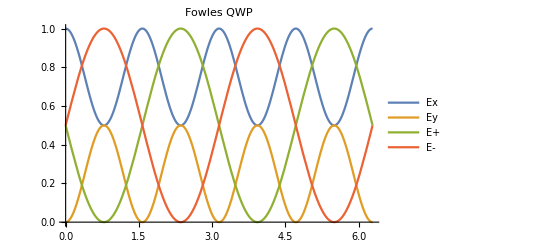

```mathematica
(*this output is the same as above up to a π phase shift between the E+/- projections, so the two definitions have different fast axis orientations*)
Eout=QWPmine[θ].Ex;
Plot[{Abs[Ex.Eout]^2,Abs[Ey.Eout]^2,Abs[Eplus.Eout]^2,Abs[Eminus.Eout]^2},{θ,0,2π},PlotLabel->"Fowles QWP",PlotLegends->{"Ex","Ey","E+","E-"}]
```

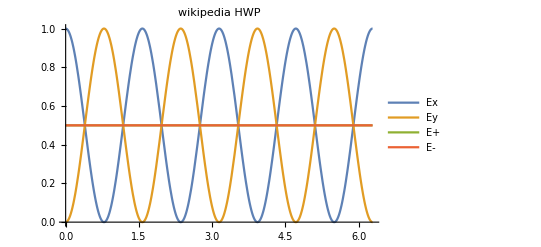

```mathematica
Eout=HWP[θ].Ex;
Plot[{Abs[Ex.Eout]^2,Abs[Ey.Eout]^2,Abs[Eplus.Eout]^2,Abs[Eminus.Eout]^2},{θ,0,2π},PlotLabel->"wikipedia HWP",PlotLegends->{"Ex","Ey","E+","E-"}]
```

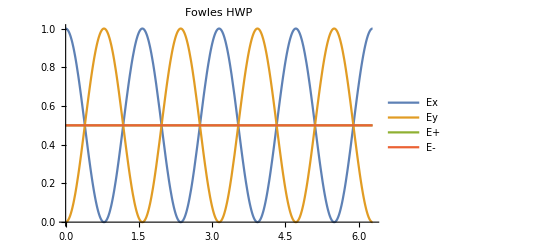

```mathematica
Eout=HWPmine[θ].Ex;
Plot[{Abs[Ex.Eout]^2,Abs[Ey.Eout]^2,Abs[Eplus.Eout]^2,Abs[Eminus.Eout]^2},{θ,0,2π},PlotLabel->"Fowles HWP",PlotLegends->{"Ex","Ey","E+","E-"}]
```

Now check the Stokes parameters

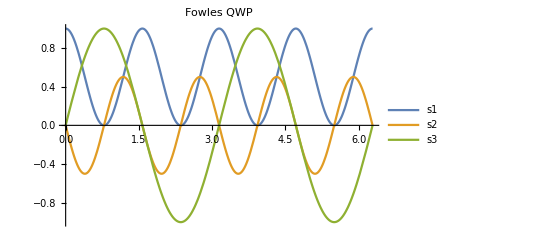

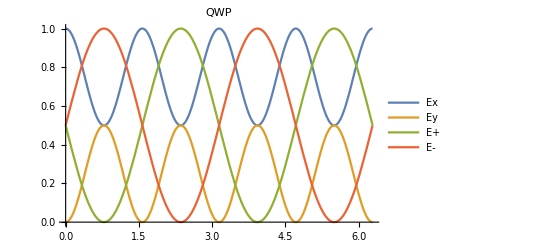

```mathematica
(*this output is the same as above up to a π phase shift between the E+/- projections, so the two definitions have different fast axis orientations*)
Eout=QWPmine[θ].Ex;
ExOut=Eout.Ex;
EyOut=Eout.Ey;
δ=Arg[EyOut]-Arg[ExOut];
s1 =Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
Plot[{s1,s2,s3},{θ,0,2π},PlotLabel->"Fowles QWP",PlotLegends->{"s1","s2","s3"}]
Plot[{Abs[Ex.Eout]^2,Abs[Ey.Eout]^2,Abs[Eplus.Eout]^2,Abs[Eminus.Eout]^2},{θ,0,2π},PlotLabel->"QWP",PlotLegends->{"Ex","Ey","E+","E-"}]
```

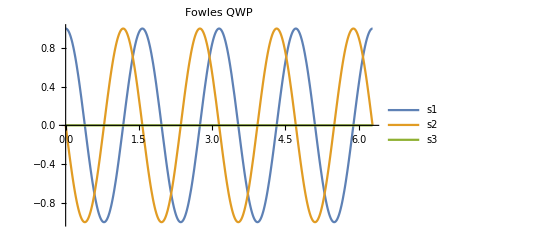

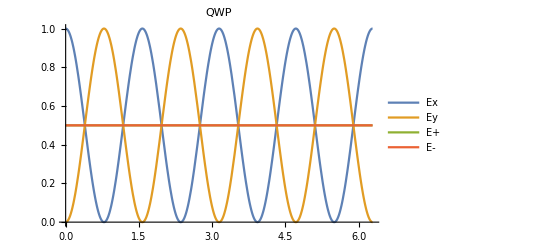

```mathematica
Eout=HWPmine[θ].Ex;
ExOut=Eout.Ex;
EyOut=Eout.Ey;
δ=Arg[EyOut]-Arg[ExOut];
s1 =Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
Plot[{s1,s2,s3},{θ,0,2π},PlotLabel->"Fowles QWP",PlotLegends->{"s1","s2","s3"}]
Plot[{Abs[Ex.Eout]^2,Abs[Ey.Eout]^2,Abs[Eplus.Eout]^2,Abs[Eminus.Eout]^2},{θ,0,2π},PlotLabel->"QWP",PlotLegends->{"Ex","Ey","E+","E-"}]
```

The non-sensical results have only shown themselves in the Poincaré sphere plot thus far, so try contour plots in case it’s an error in my function

```mathematica
Clear[θ,ϕ];
```

```mathematica
HWPmine[π/3].Ex
```

{-1/2,-(√3)/2}

```mathematica
QWPmine[0].HWPmine[π/3].Ex
```

{-1/2,-(ⅈ √3)/2}

I think everything up to here, including the plot below is behaving correctly. Note that what to expect for the Stokes parameters after the waveplate transformations depends on the order in which we apply the waveplates, i.e. the ordering of the application of the matrices to Ex below

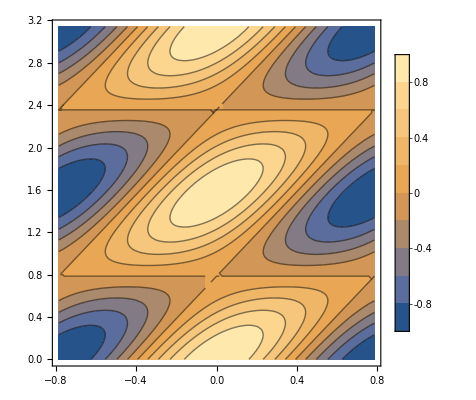

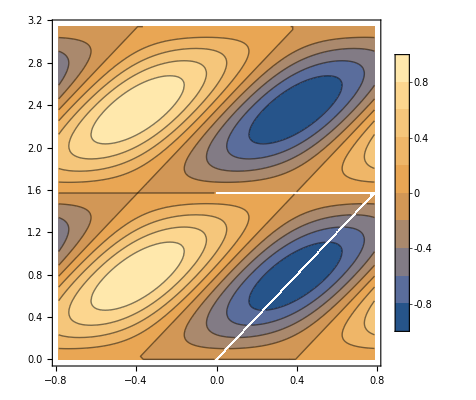

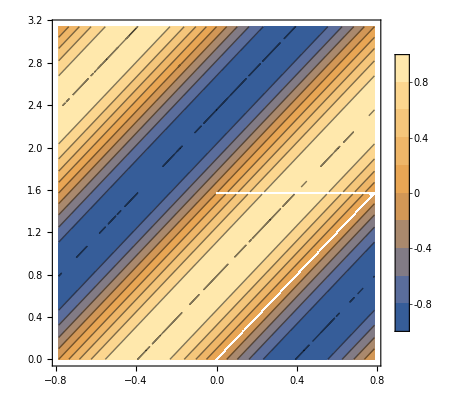

```mathematica
Eout=QWPmine[ϕ].HWPmine[θ].Ex;
ExOut=Eout.Ex;
EyOut=Eout.Ey;
δ=Arg[EyOut]-Arg[ExOut];
s1 =Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
ContourPlot[s1,{θ,-π/4,π/4},{ϕ,0,π},PlotLegends->Automatic]
ContourPlot[s2,{θ,-π/4,π/4},{ϕ,0,π},PlotLegends->Automatic]
ContourPlot[s3,{θ,-π/4,π/4},{ϕ,0,π},PlotLegends->Automatic]
```

### visualizing Stokes vector on Poincaré sphere

```mathematica
R[θ_]:=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}});
qwp=({{1, 0}, {0, ⅈ}});
hwp=({{1, 0}, {0, -1}});
QWP[θ_]:=R[θ].qwp.Inverse[R[θ]];
HWP[θ_]:=R[θ].hwp.Inverse[R[θ]];
Ex={1,0};
Ey={0,1};
Eplus=1/(√2){1,ⅈ};
Eminus=1/(√2){1,-ⅈ};
```

```mathematica
Ein=Ex;
Eout=HWP[hwpAngleDegrees π/180].QWP[qwpAngleDegrees π/180].Ein;
ExOut=Eout.Ex;
EyOut=Eout.Ey;
δ=Arg[EyOut]-Arg[ExOut];
s1 =Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
Manipulate[Evaluate[PoincareSphereVectorFromStokesParameters[s1,s2,s3]/.{qwpAngleDegrees->qwpAngle,hwpAngleDegrees->hwpAngle}],{qwpAngle,0.001,180},{hwpAngle,0.001,180}]
```

### visualizing the polarization ellipse

```mathematica
R[θ_]:=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}});
qwp=({{1, 0}, {0, ⅈ}});
hwp=({{1, 0}, {0, -1}});
QWP[θ_]:=R[θ].qwp.Inverse[R[θ]];
HWP[θ_]:=R[θ].hwp.Inverse[R[θ]];
Ex={1,0};
Ey={0,1};
Eplus=1/(√2){1,ⅈ};
Eminus=1/(√2){1,-ⅈ};
```

```mathematica
Ein=Ex;
Eout=HWP[hwpAngleDegrees π/180].QWP[qwpAngleDegrees π/180].Ein;
ExOut=Eout.Ex;
EyOut=Eout.Ey;
δ=Arg[EyOut]-Arg[ExOut];
s1 =Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
x[t_]=Abs[ExOut]Cos[t];
y[t_]=Abs[EyOut]Cos[t-δ];
Manipulate[GraphicsGrid[{{Evaluate[PoincareSphereVectorFromStokesParameters[s1,s2,s3]/.{qwpAngleDegrees->qwpAngle,hwpAngleDegrees->hwpAngle}],ParametricPlot[Evaluate[{x[t],y[t]}/.{qwpAngleDegrees->qwpAngle,hwpAngleDegrees->hwpAngle}],{t,0,2π},PlotRange->{{-1,1},{-1,1}}]}},ImageSize->Full],{qwpAngle,0.001,180},{hwpAngle,0.001,180}]
```

### plot vectors indicating the direction of the polarization ellipse

```mathematica
R[θ_]:=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}});
qwp=({{1, 0}, {0, ⅈ}});
hwp=({{1, 0}, {0, -1}});
QWP[θ_]:=R[θ].qwp.Inverse[R[θ]];
HWP[θ_]:=R[θ].hwp.Inverse[R[θ]];
Ex={1,0};
Ey={0,1};
Eplus=1/(√2){1,ⅈ};
Eminus=1/(√2){1,-ⅈ};
```

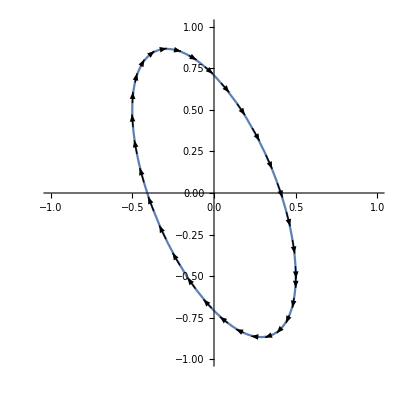

```mathematica
Ein=Ex;
Eout=HWP[π/4].QWP[π/8].Ein;
ExOut=Eout.Ex;
EyOut=Eout.Ey;
δ=Arg[EyOut]-Arg[ExOut];
s1 =Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
x[t_]=Abs[ExOut]Cos[t];
y[t_]=Abs[EyOut]Cos[t-δ];
Show[ParametricPlot[{x[t],y[t]},{t,0,2π},PlotRange->{{-1,1},{-1,1}}],
Graphics[Table[Arrow[{{x[t],y[t]},{x[t]+0.1D[x[τ],τ]/.τ->t,y[t]+0.1D[y[τ],τ]/.τ->t}}],{t,0,2π,0.2}]]]
```

```mathematica
Eout=HWP[hwpAngleDegrees π/180].QWP[qwpAngleDegrees π/180].Ein;
ExOut=Eout.Ex;
EyOut=Eout.Ey;
δ=Arg[EyOut]-Arg[ExOut];
s1 =Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
x[t_]=Abs[ExOut]Cos[t];
y[t_]=Abs[EyOut]Cos[t-δ];
Manipulate[GraphicsGrid[{{Evaluate[PoincareSphereVectorFromStokesParameters[s1,s2,s3]/.{qwpAngleDegrees->qwpAngle,hwpAngleDegrees->hwpAngle}],Show[ParametricPlot[Evaluate[{x[t],y[t]}/.{qwpAngleDegrees->qwpAngle,hwpAngleDegrees->hwpAngle}],{t,0,2π},PlotRange->{{-1,1},{-1,1}}],Table[Graphics[Arrow[{Evaluate[{x[t],y[t]}/.{qwpAngleDegrees->qwpAngle,hwpAngleDegrees->hwpAngle}],Evaluate[{x[t]-Sign[Mod[δ,π]]0.1D[x[τ],τ]/.τ->t,y[t]-Sign[Mod[δ,π]]0.1D[y[τ],τ]/.τ->t}/.{qwpAngleDegrees->qwpAngle,hwpAngleDegrees->hwpAngle}]}]],{t,0,2π,0.2}]]}},ImageSize->Full],{qwpAngle,0.001,180},{hwpAngle,0.001,180}]
```

### Manual evaluation of Stokes parameters for specific states

Manually evaluate the Stoke’s parameters for some different polarization states. Ex/yOut below are taken to be the abs of the complex amplitudes

```mathematica
δ=π/2; (*RH circular polarization*)
ExOut=EyOut=1/√2;
s1=Abs[ExOut]^2-Abs[EyOut]^2
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
"s1, s2, s3"
{s1,s2,s3}
```

0

s1, s2, s3

{0,0,1}

```mathematica
δ=-π/2; (*LH circular polarization*)
ExOut=EyOut=1/√2;
s1=Abs[ExOut]^2-Abs[EyOut]^2
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
"s1, s2, s3"
{s1,s2,s3}
```

0

s1, s2, s3

{0,0,-1}

```mathematica
δ=0; (*H polarization*)
ExOut=1;
EyOut=0;
s1=Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
"s1, s2, s3"
{s1,s2,s3}
```

s1, s2, s3

{1,0,0}

```mathematica
δ=0; (*V polarization*)
ExOut=0;
EyOut=1;
s1=Abs[ExOut]^2-Abs[EyOut]^2
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
"s1, s2, s3"
{s1,s2,s3}
```

-1

s1, s2, s3

{-1,0,0}

```mathematica
δ=π; (*diagonal polarization*)
ExOut=1/√2;
EyOut=1/√2;
s1=Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
"s1, s2, s3"
{s1,s2,s3}
```

s1, s2, s3

{0,-1,0}

```mathematica
δ=0; (*anti-diagonal polarization*)
ExOut=1/√2;
EyOut=1/√2;
s1=Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
"s1, s2, s3"
{s1,s2,s3}
```

s1, s2, s3

{0,1,0}

Now produce the states with rotations on Ex, so I can verify that Mathematica is properly getting the abs and args of the amplitudes. All of the results below seem to make sense... so what

```mathematica
R[θ_]:=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}});
qwp=({{1, 0}, {0, ⅈ}});
hwp=({{1, 0}, {0, -1}});
QWP[θ_]:=R[θ].qwp.Inverse[R[θ]];
HWP[θ_]:=R[θ].hwp.Inverse[R[θ]];
Ex={1,0};
Ey={0,1};
Eplus=1/(√2){1,ⅈ};
Eminus=1/(√2){1,-ⅈ};
```

```mathematica
(*RH circular polarization*)
{ExOut,EyOut}=QWP[π/4].Ex
δ=Arg[EyOut/ExOut]
s1=Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
"s1, s2, s3"
{s1,s2,s3}
```

{1/2+ⅈ/2,-1/2+ⅈ/2}

π/2

s1, s2, s3

{0,0,1}

```mathematica
(*LH circular polarization*)
{ExOut,EyOut}=QWP[-π/4].Ex
δ=Arg[EyOut/ExOut]
s1=Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
"s1, s2, s3"
{s1,s2,s3}
```

{1/2+ⅈ/2,1/2-ⅈ/2}

-π/2

s1, s2, s3

{0,0,-1}

```mathematica
(*V polarization*)
{ExOut,EyOut}=HWP[-π/4+10^-6].Ex//N
δ=Arg[EyOut/ExOut]
s1=Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
"s1, s2, s3"
{s1,s2,s3}
```

{2.×10^-6,1.}

0

s1, s2, s3

{-1.,4.×10^-6,0.}

```mathematica
(*D polarization. I might have A and D flipped*)
{ExOut,EyOut}=HWP[π/8].Ex//N
δ=Arg[EyOut/ExOut]
s1=Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
"s1, s2, s3"
{s1,s2,s3}
```

{0.707107,-0.707107}

π

s1, s2, s3

{-2.22045×10^-16,-1.,0.}

```mathematica
(*A polarization. I might have A and D flipped.*)
{ExOut,EyOut}=HWP[-π/8].Ex//N
δ=Arg[EyOut/ExOut]
s1=Abs[ExOut]^2-Abs[EyOut]^2;
s2 =2Abs[ExOut]Abs[EyOut]Cos[δ];
s3 =2Abs[ExOut]Abs[EyOut]Sin[δ];
"s1, s2, s3"
{s1,s2,s3}
```

{0.707107,0.707107}

0

s1, s2, s3

{-2.22045×10^-16,1.,0.}